```mathematica
v=9;
Logmaxdvdd[v]
Logvvpmaxdvdd[v]
pmaxdvdd[v]
```

```mathematica
Logmaxdvdd[v]={{Log[5000],5.358169631350033},{Log[10000],5.167567815298064},{Log[20000],4.961401281440647},{Log[30000],4.857775447451913},{Log[50000],4.774807469779157}};
```

```mathematica
Logvvpmaxdvdd[v]={{Log[5000],2.1473556335766033},{Log[10000],2.156363230189808},{Log[20000],2.158432927677586},{Log[30000],2.1625261565205056},{Log[50000],2.16397453751852}};
```

```mathematica
pmaxdvdd[v]={{5000,0.0853},{10000,0.08410000000000001},{20000,0.0835},{30000,0.08310000000000001},{50000,0.0829}};
```

```mathematica
ν=1/0.09;
k0=0.08122;
ClearAll[a0,b0,d0,ex0,c0]
model1=a0*x-b0;
model2=d0+c0*x^(-ex0)
model3=d0+c0*x^(-1/ν)
model4=k0+c0*x^(-ex0)

nlf1=NonlinearModelFit[Logvvpmaxdvdd[v],model,{a0,b0},x];

nlf1[{"BestFit","ParameterTable"}]


nlf2=NonlinearModelFit[pmaxdvdd[v],model2,{d0,c0,ex0},x];

nlf2[{"BestFit","ParameterTable"}]


nlf3=NonlinearModelFit[pmaxdvdd[v],model3,{d0,c0},x];

nlf3[{"BestFit","ParameterTable"}]


nlf4=NonlinearModelFit[pmaxdvdd[v],model4,{ex0,c0},x];

nlf4[{"BestFit","ParameterTable"}]
```

d0+c0 x^-ex0

d0+c0/x^0.09

0.08122+c0 x^-ex0

{2.0896+0.00698666 x, | Estimate | Standard Error | t-Statistic | P-Value
a0 | 2.0896 | 0.0104778 | 199.43 | 2.78009×10^-7
b0 | -0.00698666 | 0.00107074 | -6.52511 | 0.00731399}

{0.08378-442.061/x^55.2964, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.08378 | 0.000610574 | 137.215 | 0.0000531081
c0 | -442.061 | 0. | -∞ | 0.
ex0 | 55.2964 | 0. | ∞ | 0.}

{0.0722858+0.027573/x^0.09, | Estimate | Standard Error | t-Statistic | P-Value
d0 | 0.0722858 | 0.00135178 | 53.4745 | 0.000014404
c0 | 0.027573 | 0.00323399 | 8.52601 | 0.00338948}

{0.08122+0.130032/x^0.408622, | Estimate | Standard Error | t-Statistic | P-Value
ex0 | 0.408622 | 0.0252883 | 16.1586 | 0.000515593
c0 | 0.130032 | 0.030431 | 4.273 | 0.0235312}

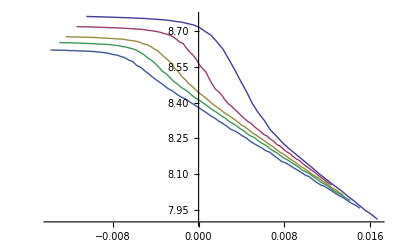

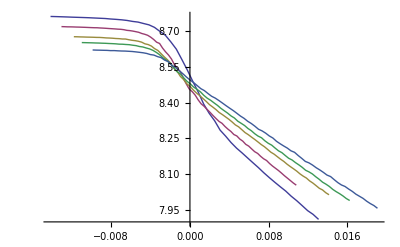

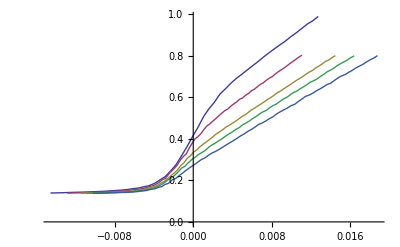

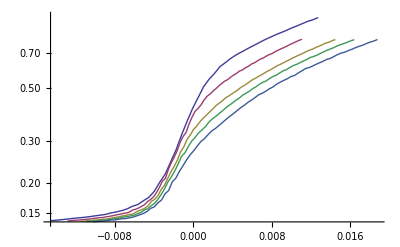

```mathematica
b0=0.12;
k01=nlf2["ParameterTableEntries"][[1]][[1]];
k02=nlf3["ParameterTableEntries"][[1]][[1]];
k03=k0;
ex01=-nlf2["ParameterTableEntries"][[3]][[1]];
ex02=-1/ν;
ex03=-nlf4["ParameterTableEntries"][[1]][[1]];
a=-nlf1["ParameterTableEntries"][[2]][[1]];
c01=nlf2["ParameterTableEntries"][[2]][[1]];
c02=nlf3["ParameterTableEntries"][[2]][[1]];
c03=nlf4["ParameterTableEntries"][[2]][[1]];


Do[

(*absMs1[l]=Table[{(absM[l][[All,1]][[i]]),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs2[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(ex0))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

absMs[l]=Table[{(absM[l][[All,1]][[i]]-(k0+c0*l^(ex0)))*l^b,absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];*)

vels1[v][l]=Table[{(vel[v][l][[All,1]][[i]]-(k01+c01*(l*1000)^(ex01)))*(l*1000)^b0,vel[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[vel[v][l]]}];

vels2[v][l]=Table[{(vel[v][l][[All,1]][[i]]-(k02+c02*(l*1000)^(ex02)))*(l*1000)^b0,vel[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[vel[v][l]]}];

vels3[v][l]=Table[{(vel[v][l][[All,1]][[i]]-(k03+c03*(l*1000)^(ex03)))*(l*1000)^b0,(v-vel[v][l][[All,2]][[i]])*l^(-a)},{i,1,Length[vel[v][l]]}];

,{l,{5,10,20,30,50}}]
(*ListLogPlot[{absM[16],absM[24],absM[32],absM[48],absM[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs1[16],absMs1[24],absMs1[32],absMs1[48],absMs1[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs2[16],absMs2[24],absMs2[32],absMs2[48],absMs2[64]},Joined->True,PlotMarkers->Automatic]
ListPlot[{absMs[16],absMs[24],absMs[32],absMs[48],absMs[64]},Joined->True,PlotMarkers->Automatic]*)
ListPlot[{vels1[v][5],vels1[v][10],vels1[v][20],vels1[v][30],vels1[v][50]},Joined->True]
ListPlot[{vels2[v][5],vels2[v][10],vels2[v][20],vels2[v][30],vels2[v][50]},Joined->True]
ListPlot[{vels3[v][5],vels3[v][10],vels3[v][20],vels3[v][30],vels3[v][50]},Joined->True]
ListLogPlot[{vels3[v][5],vels3[v][10],vels3[v][20],vels3[v][30],vels3[v][50]},Joined->True]
```

```mathematica
l1=10;
l2=50;

Do[
(*input1[l]=Table[{(absM[l][[All,1]][[i]]-(k01+c01*l^(ex01))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

input2[l]=Table[{(absM[l][[All,1]][[i]]-(k02+c02*l^(ex02))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];*)

input3[l]=Table[{(vel[v][l][[All,1]][[i]]-(k03+c03*(l*1000)^(ex03))),vel[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[vel[v][l]]}];
,{l,{l1,l2}}]
sum={};

aux=1000;
For[z=-0.4,z<0.4,z+=0.01,
ClearAll[i];

Do[
dat[l]=Table[{input3[l][[All,1]][[i]]*(l*1000)^z,(input3[l][[All,2]][[i]])},{i,1,Length[input3[l]]}];
i[l]=Interpolation[dat[l]]
,{l,{l1,l2}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]]];

val=NIntegrate[Abs[i[l1][x]-i[l2][x]],{x,min,max}]/(max-min);
(*Print[val]*)

sum=Append[sum,{z,val}];

If[val<aux,
aux=val;
zf=z;
]
]

aux
"= zf"zf
```

0.0296144

-0.12 = zf

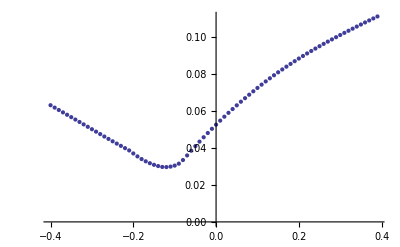

```mathematica
ListPlot[sum]
```

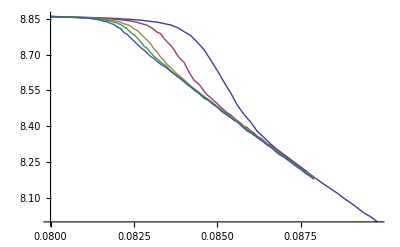

```mathematica
ListPlot[{vel[v][5],vel[v][10],vel[v][20],vel[v][30],vel[v][50]},Joined->True]
```

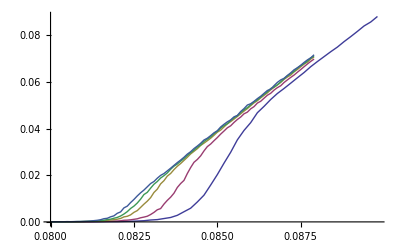

```mathematica
ListPlot[{gap[v][5],gap[v][10],gap[v][20],gap[v][30],gap[v][50]},Joined->True]
```

```mathematica
l1=5;
l2=20;
l3=30;
l4=50;
sum={};

Do[
(*input1[l]=Table[{(absM[l][[All,1]][[i]]-(k01+c01*l^(ex01))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];

input2[l]=Table[{(absM[l][[All,1]][[i]]-(k02+c02*l^(ex02))),absM[l][[All,2]][[i]]*l^(-a)},{i,1,Length[absM[l]]}];*)

input3[l]=Table[{(vel[v][l][[All,1]][[i]]-(k03+c03*(l*1000)^(ex03))),vel[v][l][[All,2]][[i]]*l^(-a)},{i,1,Length[vel[v][l]]}];
,{l,{l1,l2,l3,l4}}]

aux=1000;
For[z=-0.4,z<0.4,z+=0.01,
ClearAll[i];

Do[
dat[l]=Table[{input3[l][[All,1]][[i]]*(l*1000)^z,input3[l][[All,2]][[i]]},{i,1,Length[input3[l]]}];
i[l]=Interpolation[dat[l]]
,{l,{l1,l2,l3,l4}}];


min=Max[dat[l1][[All,1]][[1]],dat[l2][[All,1]][[1]],dat[l3][[All,1]][[1]],dat[l4][[All,1]][[1]]];
max=Min[dat[l1][[All,1]][[Length[dat[l1]]]],dat[l2][[All,1]][[Length[dat[l2]]]],dat[l3][[All,1]][[Length[dat[l3]]]],dat[l4][[All,1]][[Length[dat[l4]]]]];

val=NIntegrate[Abs[Max[i[l1][x],i[l2][x],i[l3][x],i[l4][x]]-Min[i[l1][x],i[l2][x],i[l3][x],i[l4][x]]],{x,min,max}]/(max-min);
(*Print[val]*)
sum=Append[sum,{z,val}];

If[val<aux,
aux=val;
zf=z;
]
]

aux
"= zf"zf
```

0.0462425

-0.22 = zf

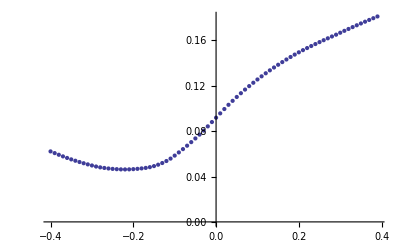

```mathematica
ListPlot[sum]
```